# Linear Chiral (E_1=eV_g,E_2=2 eV_g)(Voltage probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1.05*10^(-34);
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=0.4*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11-(G13*(G31))/(G33);
LeT=L11-(G13*L31)/G33;
LhV=π11-(π13*G31)/G33;
LhT=K11-(π13*L31)/G33;
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,x2,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
},{x1,0,0.020,0.0001}];//AbsoluteTiming
list=Sort[list1];
Export["check1.dat",list]
```

{49.2013,Null}

check1.dat

# Linear Chiral (E_1=eV_g,E_2=2 eV_g)(Voltage temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=10.40*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
},{x1,0,0.238,0.001}];//AbsoluteTiming
list=Sort[list1];
Export["check2.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained 0.0000304442 and 9.673×10^-9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -9.26122×10^-10 and 2.85132×10^-12 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.3798}. NIntegrate obtained -0.000030444 and 9.87254×10^-9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{63.6633,Null}

check2.dat

# Linear Helical (E_1=eV_g,E_2=2 eV_g)(Voltage probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
θ=1;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=1.5*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11-(G13*(G31))/(G33);
LeT=L11-(G13*L31)/G33;
LhV=π11-(π13*G31)/G33;
LhT=K11-(π13*L31)/G33;
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,Jq*h/(kb^2*θ*δT),Subscript[η, r]}]
},{x1,0,0.035,0.0001}];//AbsoluteTiming
list=Sort[list1];
Export["check3.dat",list]
```

{27.7057,Null}

check3.dat

# Linear Helical (E_1=eV_g,E_2=2 eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=10.20*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,Jq*h/(kb^2*θ*δT),Subscript[η, r]}]
},{x1,0,0.238,0.001}];//AbsoluteTiming
list=Sort[list1];
Export["check4.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained 0.0000743693 and 1.28451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.1744}. NIntegrate obtained -1.37996×10^-9 and 3.67529×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.1324}. NIntegrate obtained -0.0000743691 and 1.2865×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{21.8266,Null}

check4.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

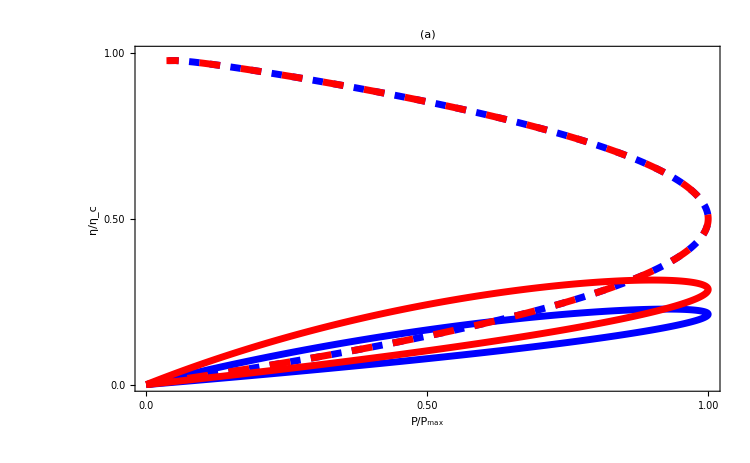

```mathematica
data1=Import["check1.dat"][[All,{4,5}]];
data2=Import["check2.dat"][[All,{3,4}]];
data3=Import["check3.dat"][[All,{3,4}]];
data4=Import["check4.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

# Non-linear chiral (E_1=eV_g,E_2=2 eV_g)(Voltage probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=2Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,P/(0.316493),2*η}];
},{Vg,0,10,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check11.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.07908×10^-14 and 3.06773×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.01853×10^-12 and 5.75998×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.07908×10^-14 and 3.06773×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.01853×10^-12 and 5.75998×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.25261×10^-17 and 2.97945×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.15573×10^-18 and 5.8979×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.28035×10^-16 and 1.38734×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.28035×10^-16 and 1.38734×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.00107×10^-16 and 1.45084×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.60171×10^-16 and 5.58054×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.60171×10^-16 and 5.58054×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.47605×10^-17 and 6.07384×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.69153×10^-16 and 2.56922×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.69153×10^-16 and 2.56922×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.23497×10^-18 and 2.90434×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.50486×10^-17 and 1.11836×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.50486×10^-17 and 1.11836×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.05358×10^-17 and 1.04408×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.53771×10^-18 and 4.28645×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.53771×10^-18 and 4.28645×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.7293×10^-17 and 5.11917×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.62704×10^-18 and 1.63536×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.78629×10^-19 and 1.71061×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.14588×10^-18 and 1.71505×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05723×10^-19 and 9.92171×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.50571×10^-21 and 9.9387×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.78674×10^-19 and 9.2491×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.32572×10^-20 and 4.89157×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.57509×10^-20 and 3.62245×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.84091×10^-20 and 4.66435×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.39322×10^-21 and 1.42308×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.15046×10^-20 and 1.55806×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.78518×10^-20 and 1.79559×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{295.908,Null}

check11.dat

# Non-linear chiral (E_1=eV_g,E_2=2 eV_g)(Voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=2Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(0.316493),2*η}];
},{Vg,0,10,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check12.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.05252×10^-20 and 2.19433×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.05252×10^-20 and 2.19433×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.34224×10^-17 and 7.80795×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76747×10^-13 and 1.97659×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.51956×10^-16 and 1.94517×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.50389×10^-16 and 5.79789×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.7036×10^-17 and 7.23721×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1672×10^-16 and 2.68432×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65382×10^-16 and 7.21809×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.90908×10^-17 and 3.63336×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.27364×10^-16 and 1.65443×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.26674×10^-17 and 7.50736×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08544×10^-17 and 2.16605×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.19646×10^-16 and 1.21941×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2602×10^-13 and 1.29256×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.57527×10^-19 and 1.13071×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.35663×10^-18 and 5.92694×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.75428×10^-17 and 7.02383×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.51328×10^-18 and 3.10565×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.83411×10^-17 and 2.15215×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5918×10^-18 and 3.02192×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32549×10^-18 and 1.54627×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4663×10^-17 and 1.12637×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2294×10^-18 and 1.52289×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03255×10^-17 and 5.36767×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1164×10^-17 and 3.46561×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57485×10^-18 and 7.69184×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.72908×10^-19 and 3.11143×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.61647×10^-18 and 2.44866×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.1122×10^-19 and 3.16429×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.88176×10^-14 and 2.3185×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57179×10^-13 and 1.95234×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.54511×10^-19 and 1.49468×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03346×10^-14 and 7.42324×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63104×10^-14 and 5.62076×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.37514×10^-14 and 3.78627×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.13531×10^-15 and 2.45091×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.87123×10^-15 and 2.23939×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.75278×10^-15 and 2.92807×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.77542×10^-16 and 1.26133×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2586×10^-15 and 1.18274×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.78534×10^-15 and 1.17226×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{950.274,Null}

check12.dat

# Non-linear helical (E_1=eV_g,E_2=2 eV_g)(Voltage probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=2*Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,P/(0.316493),2*η}];
},{Vg,0,10,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check13.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.25749×10^-14 and 5.91137×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00903×10^-16 and 3.47717×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.25749×10^-14 and 5.91137×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00903×10^-16 and 3.47717×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.04731×10^-17 and 6.33392×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.08111×10^-16 and 3.48367×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.84197×10^-14 and 1.87969×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.84197×10^-14 and 1.87969×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.1796×10^-17 and 1.90529×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.49358×10^-14 and 7.48991×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.49358×10^-14 and 7.48991×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.93651×10^-18 and 8.29381×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.6216×10^-15 and 5.38715×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.6216×10^-15 and 5.38715×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.59142×10^-18 and 5.75168×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.85416×10^-16 and 1.9989×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.85416×10^-16 and 1.9989×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.04422×10^-17 and 2.12903×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.39566×10^-17 and 9.33391×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.39566×10^-17 and 9.33391×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.88649×10^-17 and 9.96944×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.56095×10^-18 and 3.24005×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.56095×10^-18 and 3.24005×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.15996×10^-18 and 4.20871×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.01494×10^-19 and 1.35683×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.73068×10^-19 and 1.58733×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.38713×10^-19 and 1.61274×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.11491×10^-19 and 8.55747×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.10911×10^-19 and 8.50184×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.25959×10^-19 and 8.95194×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.56304×10^-19 and 3.16841×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.06464×10^-20 and 3.46411×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.64809×10^-20 and 4.18481×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.81517×10^-20 and 1.84172×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.29228×10^-20 and 1.2075×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.89259×10^-21 and 1.2794×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{314.456,Null}

check13.dat

# Non-linear helical (E_1=eV_g,E_2=2 eV_g)(Voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=2*Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(0.316493),2*η}];
},{Vg,0,10,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check14.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91935×10^-13 and 2.62259×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3633×10^-13 and 1.74909×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.03491×10^-13 and 7.74262×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.92202×10^-13 and 5.68935×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.29213×10^-13 and 2.45133×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.64426×10^-13 and 1.63287×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26565×10^-14 and 1.2444×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.44128×10^-13 and 3.71532×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.54117×10^-15 and 1.25091×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.96268×10^-15 and 7.06562×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32707×10^-14 and 2.66406×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.71924×10^-15 and 7.59724×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62381×10^-16 and 4.41608×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.54366×10^-15 and 1.97464×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.79551×10^-16 and 4.0831×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.80292×10^-16 and 1.74191×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.31735×10^-15 and 8.46066×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.8708×10^-16 and 1.50196×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.93732×10^-17 and 3.88504×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.37992×10^-16 and 2.56305×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1525×10^-17 and 4.03478×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.13312×10^-17 and 3.61128×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02859×10^-16 and 2.46254×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.78363×10^-17 and 3.22806×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2313×10^-18 and 1.51581×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.19101×10^-17 and 1.1649×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.65171×10^-18 and 8.82976×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.07976×10^-19 and 8.40008×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.14508×10^-18 and 6.4644×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57689×10^-18 and 7.28676×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.72722×10^-15 and 1.54219×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.26144×10^-14 and 1.33733×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.82277×10^-14 and 6.19262×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31678×10^-18 and 3.37×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.24366×10^-17 and 2.84504×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.89183×10^-19 and 1.19694×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.61833×10^-15 and 7.23383×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.14865×10^-15 and 5.37917×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.25567×10^-15 and 5.68755×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08863×10^-16 and 1.20465×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.72758×10^-16 and 1.17584×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.7355×10^-16 and 2.89972×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06156×10^-17 and 1.31899×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91949×10^-17 and 1.1672×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.16112×10^-17 and 1.19539×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1135.42,Null}

check14.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

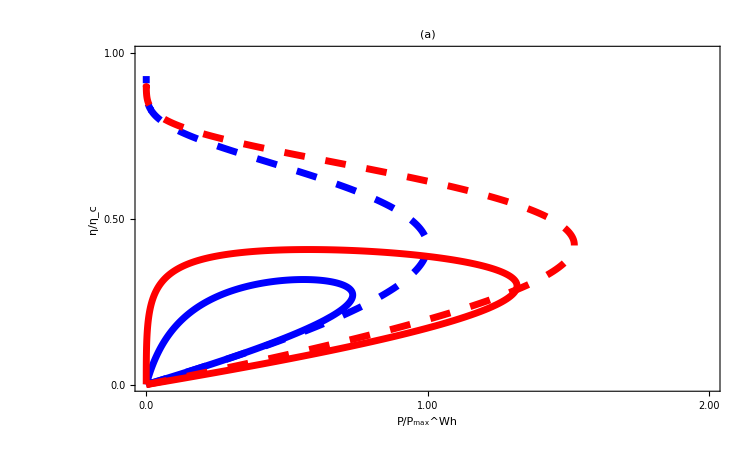

```mathematica
data1=Import["check11.dat"][[All,{3,4}]];
data2=Import["check12.dat"][[All,{4,5}]];
data3=Import["check13.dat"][[All,{3,4}]];
data4=Import["check14.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,2},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

# Linear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
θ=1;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=1.5*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11-(G13*(G31))/(G33);
LeT=L11-(G13*L31)/G33;
LhV=π11-(π13*G31)/G33;
LhT=K11-(π13*L31)/G33;
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*10;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/0.67,-J1/Jq,ηr1}]
},{x1,0.020,10,0.001}];//AbsoluteTiming
list=Sort[list1];
Export["check30.dat",list]
```

{643.862,Null}

check30.dat

# Linear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=9.80*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/(2.15*10^-7),-J1/Jq,ηr1}]
},{x1,0.205671,4,0.001}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained 0.000110944 and 1.83076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.3973}. NIntegrate obtained -3.07614×10^-9 and 1.96734×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.66844}. NIntegrate obtained -0.000110936 and 1.87762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{260.67,Null}

check40.dat

```mathematica
data1=Import["check1.dat"][[All,{4,5}]];
data2=Import["check2.dat"][[All,{3,4}]];
data3=Import["check3.dat"][[All,{3,4}]];
data4=Import["check4.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

-Graphics-

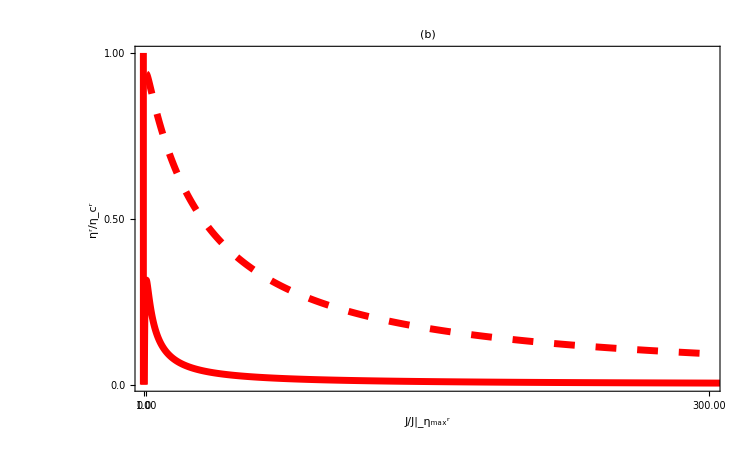

```mathematica
data1=Import["check30.dat"][[All,{5,6}]];
data2=Import["check40.dat"][[All,{5,6}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{1.00001,300},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0001,"1.00"},{0,"0.0"},{300,"300.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

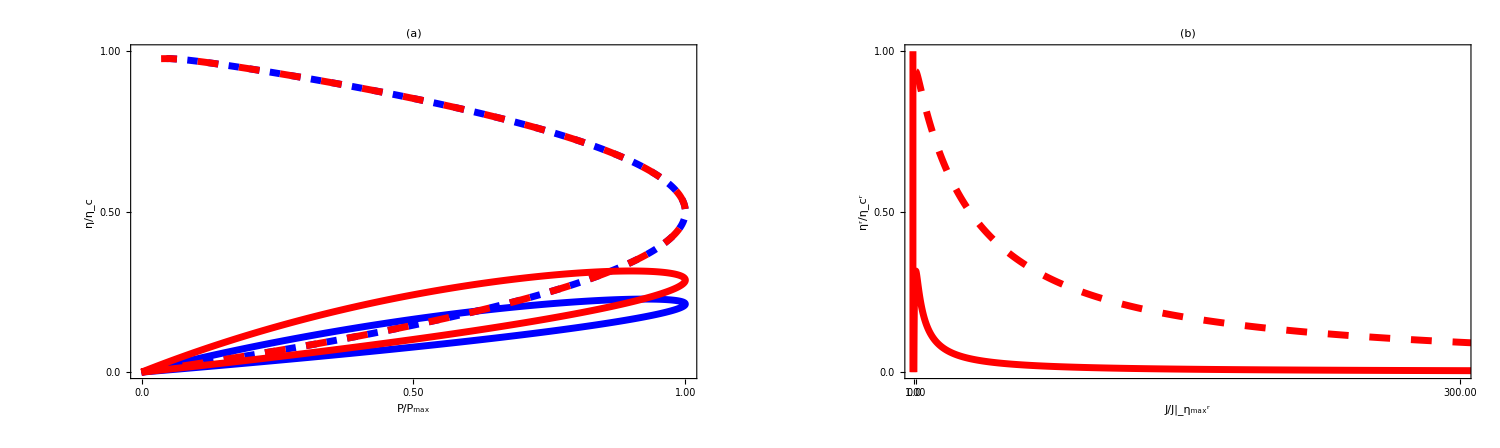

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral(VP)",Bold,Black,35],Style["Helical(VP)",Bold,Black,35],Style["Chiral(VTP)",Bold,Black,35],Style["Helical(VTP)",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3.pdf

```mathematica
kb=1.38*10^(-23);
T=0.1;
θ=0.1;
h=6.634*10^(-34);
ec=1.6*10^(-19);
μ=0;
hb=1.05*10^(-34);
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=5.20*a/ec;
V=x1*a/ec;
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=μ-0.1*ae;
n1=μ+0.1*ae;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1))
```

0.93994

```mathematica
V=LhT/LhV(1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))*0.01
```

9.68342×10^-6

```mathematica
(ec*V)/a
```

1.12271

```mathematica
V=x1*a/ec;
x1=1.1227;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
ηr1=J1/(V*I1)*0.1
```

0.93994

```mathematica
kb=1.38*10^(-23);
T=0.1;
h=6.634*10^(-34);
ec=1.6*10^(-19);
μ=0;
θ=0.1;
hb=1.05*10^(-34);
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=0.8*a/ec;
V=x1*a/ec;
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=μ-0.1*ae;
n1=μ+0.1*ae;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11-(G13*(G31))/(G33);
LeT=L11-(G13*L31)/G33;
LhV=π11-(π13*G31)/G33;
LhT=K11-(π13*L31)/G33;
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*10;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1))
```

0.283339

```mathematica
V=LhT/LhV(1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))*0.01
```

4.47361×10^-6

```mathematica
(ec*V)/a
```

0.51868

```mathematica
(J1/(V*I1)*0.1)/.{x1->0.51868}
```

0.283339

# Nonlinear chiral refrigerator (E_1=V_g,E_2=2 V_g)(voltage probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(0.82),η}];
},{Vg,0,7.5,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check50.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.84892×10^-18 and 3.99535×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.92305×10^-14 and 1.2658×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.92305×10^-14 and 1.2658×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{24.0293,Null}

check50.dat

# Nonlinear chiral refrigerator (E_1=V_g,E_2=2 V_g)(voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{Vg,P/(0.316493),-J1/0.82,ηr}];
},{Vg,0.0,9.20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check60.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.35828×10^-18 and 1.25561×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.89684×10^-18 and 1.27272×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.0637×10^-17 and 5.39005×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.58709×10^-15 and 8.33653×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.61121×10^-15 and 1.11913×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{182.702,Null}

check60.dat

# Nonlinear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(0.82),η}];
},{Vg,0,7.20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check70.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.72966×10^-17 and 9.26658×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.10152×10^-18 and 1.80887×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3473×10^-17 and 1.98658×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00035×10^-17 and 1.76508×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.45653×10^-15 and 1.35994×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.30408×10^-15 and 1.56712×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.56864×10^-13 and 4.01233×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.56864×10^-13 and 4.01233×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.45389×10^-19 and 4.65375×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.92458×10^-15 and 9.81972×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.92458×10^-15 and 9.81972×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.28699×10^-20 and 5.65929×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.41805×10^-18 and 1.69186×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.41805×10^-18 and 1.69186×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.61466×10^-20 and 1.30987×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.21399×10^-20 and 2.0364×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.11279×10^-19 and 2.25291×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.74924×10^-20 and 2.17655×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{31.4329,Null}

check70.dat

# Nonlinear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}}];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(0.82),η}];
},{Vg,0,9.20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check80.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.72747×10^-15 and 1.29216×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.36745×10^-17 and 1.21734×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.66336×10^-15 and 2.14988×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.36173×10^-17 and 2.49139×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.72747×10^-15 and 1.29216×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.93551×10^-17 and 9.52974×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.80711×10^-17 and 1.09547×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.05989×10^-16 and 7.04899×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.80711×10^-17 and 1.09547×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.48993×10^-18 and 1.70889×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.16789×10^-17 and 1.15785×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.48944×10^-17 and 1.30189×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63713×10^-16 and 1.69573×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63713×10^-16 and 1.69573×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.42277×10^-20 and 1.27053×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.0557×10^-19 and 2.50667×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.81226×10^-19 and 1.39815×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.6076×10^-19 and 1.65457×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.57455×10^-21 and 1.08342×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{84.5819,Null}

check80.dat

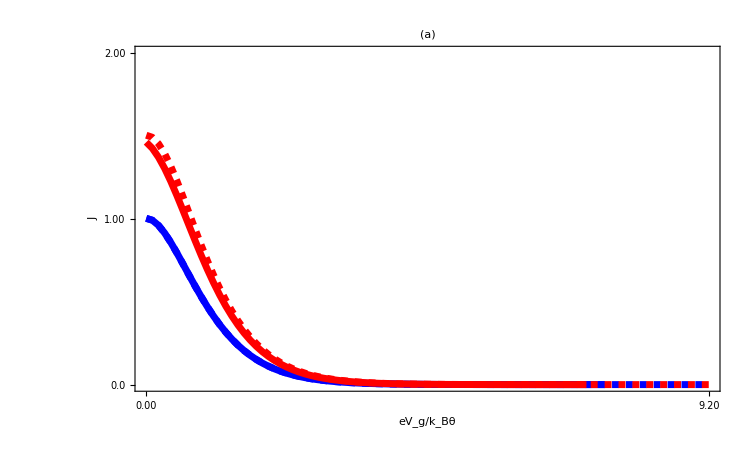

```mathematica
data1=Import["check50.dat"][[All,{1,3}]];
data2=Import["check60.dat"][[All,{1,3}]];
data3=Import["check70.dat"][[All,{1,3}]];
data4=Import["check80.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0,9.20},{0,2}},Frame->True,FrameTicks->{{{{0,"0.0"},{1,"1.00"},{2,"2.00"}},None},{{{0,"0.00"},{9.20,"9.20"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["J",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,Dashed]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

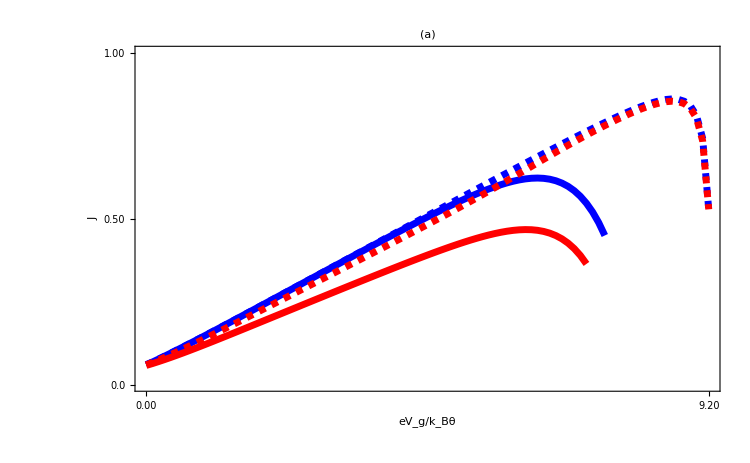

```mathematica
data1=Import["check50.dat"][[All,{1,4}]];
data2=Import["check60.dat"][[All,{1,4}]];
data3=Import["check70.dat"][[All,{1,4}]];
data4=Import["check80.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0,9.20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{0,"0.00"},{9.20,"9.20"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["J",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,Dashed]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

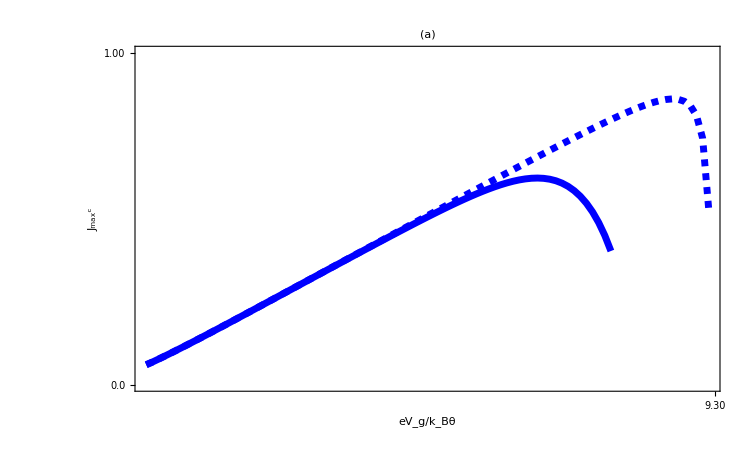

```mathematica
data1=Import["check50.dat"][[All,{1,4}]];
data2=Import["check60.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,9.20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{1,"1.00"},{2,"2.00"}},None},{{{-1,"-1.00"},{9.30,"9.30"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["J_max^c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,Dashed]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

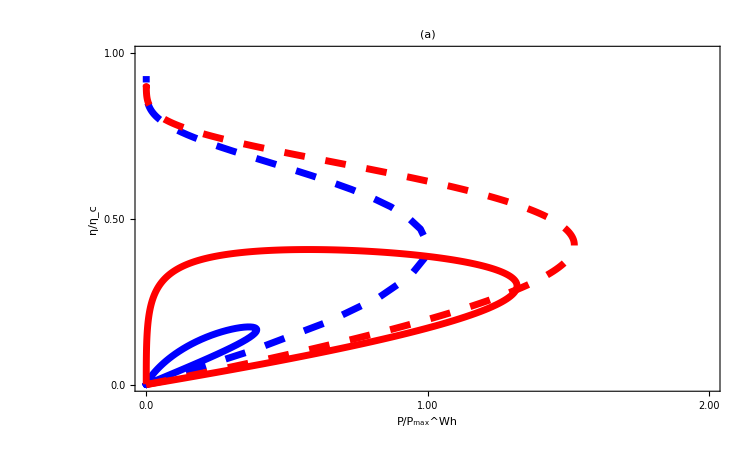

```mathematica
data1=Import["check11.dat"][[All,{3,4}]];
data2=Import["check12.dat"][[All,{4,5}]];
data3=Import["check13.dat"][[All,{3,4}]];
data4=Import["check14.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,2},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

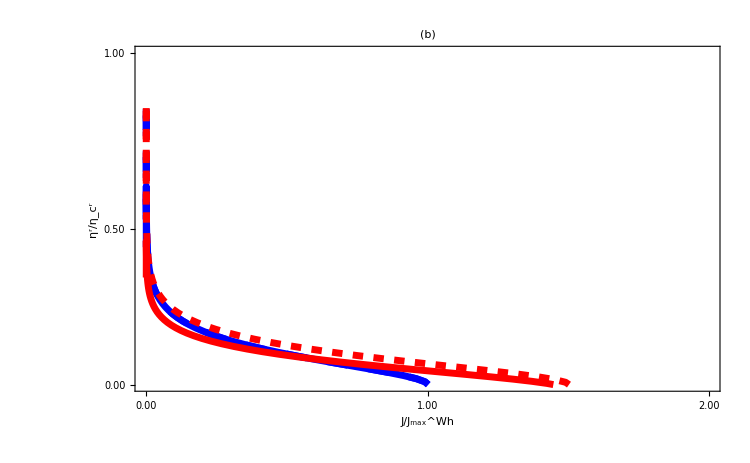

```mathematica
data1=Import["check50.dat"][[All,{3,4}]];
data2=Import["check60.dat"][[All,{3,4}]];
data3=Import["check70.dat"][[All,{3,4}]];
data4=Import["check80.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.00,2},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.00"},{1,"1.00"},{0.50,"0.50"}},None},{{{0,"0.00"},{1,"1.00"},{2,"2.00"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

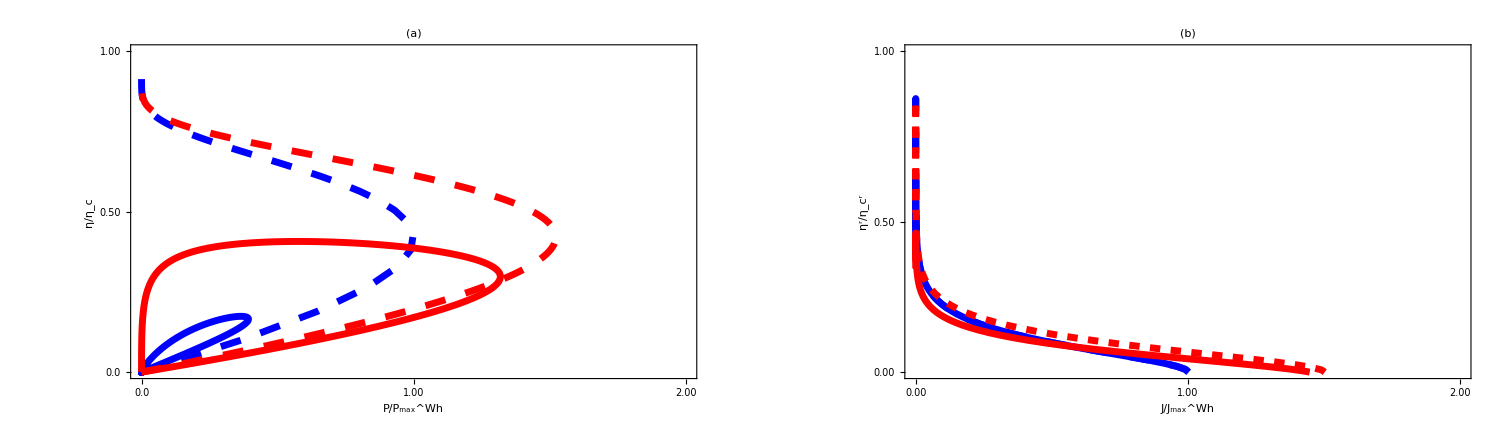

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral(VP)",Bold,Black,35],Style["Helical(VP)",Bold,Black,35],Style["Chiral(VTP)",Bold,Black,35],Style["Helical(VTP)",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf

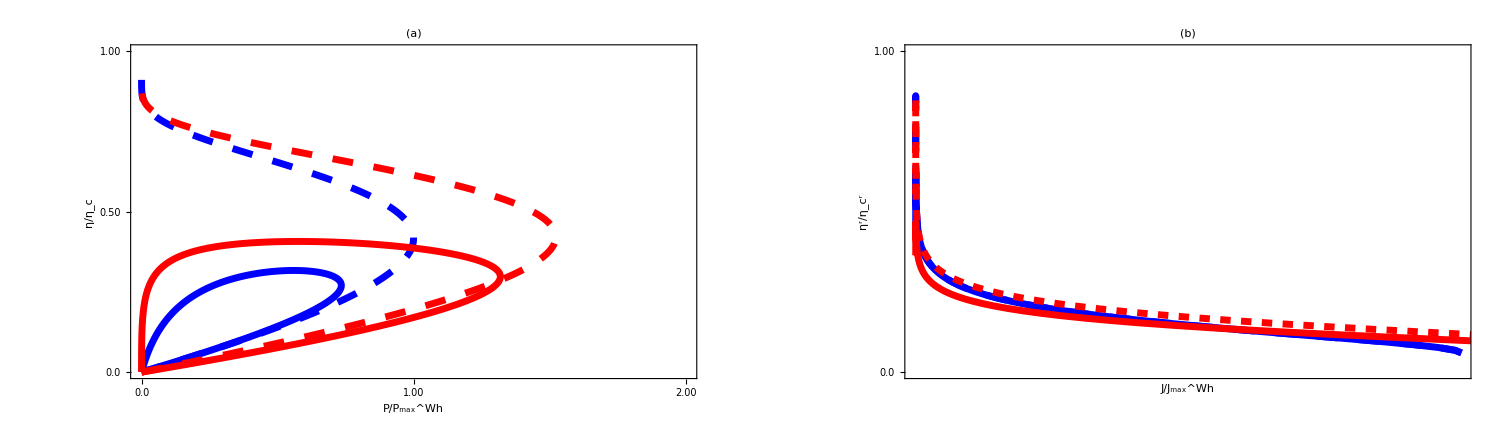

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{"Chiral(VP)","Helical(VP)","Chiral(VTP)","Helical(VTP)"},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral(VP)",Bold,Black,35],Style["Helical(VP)",Bold,Black,35],Style["Chiral(VTP)",Bold,Black,35],Style["Helical(VTP)",Bold,Black,35]},LegendFunction->(Framed[Style[#,20]]&),LegendLayout->"Row"],{0.5,0.0}]]
```

-Graphics-